## m=0.2 λ=0.1 k=0,..,0.4

0.1 | 0.421132-0.138661 ⅈ | 0.359967-0.459135 ⅈ
0.2 | 0.499085-0.177579 ⅈ | 0.425757-0.58425 ⅈ
0.3 | 0.606939-0.234139 ⅈ | 0.515779-0.766551 ⅈ
0.4 | 0.763475-0.321015 ⅈ | 0.645001-1.04727 ⅈ

{0.1,0.2,0.3,0.4}

{0.421132-0.138661 ⅈ,0.499085-0.177579 ⅈ,0.606939-0.234139 ⅈ,0.763475-0.321015 ⅈ}

{0.359967-0.459135 ⅈ,0.425757-0.58425 ⅈ,0.515779-0.766551 ⅈ,0.645001-1.04727 ⅈ}

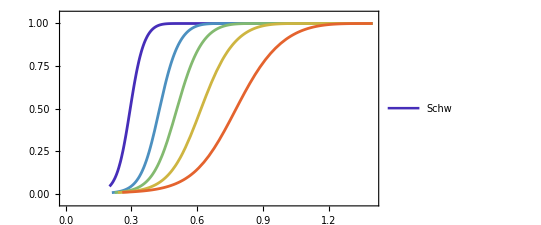

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01m02.pdf

```mathematica
Clear["Global`*"]
<<MaTeX`

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

(*fixed lambda,varying k*)
lambdaVal=0.1;

kValues={0.1,0.2,0.3,0.4};


(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;


(*Scalar perturbation potential*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r + 0.2^2)];


(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];


(* ======================================================*)
(*Position of potential maximum*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum at boundary"];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];


(* ======================================================*)
(*Third-order WKB QNM*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];


(* ======================================================*)
(*QNM data varying k*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lambdaVal,0,lval,k,Mval];
w1=QNMFrequency[lambdaVal,1,lval,k,Mval];
{k,w0,w1}],{k,kValues}];


QNMData//TableForm


kClean=QNMData[[All,1]]

w0List=QNMData[[All,2]]
w1List=QNMData[[All,3]]


(* ======================================================*)
(*Schwarzschild reference*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;

wsch1=0.26221187146850566-0.3074323472728198 I;


(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2) (1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0]) (1+((Re[w0]-Re[w1])Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1])Re[w0]^2)/(12 Im[w0]^3))];


GBFactor[x_]:=1/(1+Exp[2 I Pi x]);


Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];


(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];


GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];


TransmissionList=Transmission/@GBList;

mval=0.2;

omegaThreshold[k_]:=mval/Sqrt[1-k];
omegaThresholdSchw=mval;


(*Schwarzschild reference*)
schwPlot=Plot[Transmission[GBSch][ω],{ω,omegaThresholdSchw,1.4},PlotRange->All,PlotStyle->Directive[ColorData["Rainbow"][0.1],Thickness[0.005]]];


(*k-dependent curves*)
massivePlots=Table[Plot[TransmissionList[[i]][ω],{ω,omegaThreshold[kClean[[i]]],1.4},PlotRange->All,PlotStyle->Directive[ColorData["Rainbow"][0.1+0.2 i],Thickness[0.005]]],{i,Length[kClean]}];


GBFlambd01m02=Legended[Show[Prepend[massivePlots,schwPlot],PlotRange->{{0,1.4},{-0.05,1.05}},Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{FontFamily->"Times"},AspectRatio->9/16],Placed[LineLegend[Join[{Directive[ColorData["Rainbow"][0.1],Thickness[0.005]]},Table[Directive[ColorData["Rainbow"][0.1+0.2 i],Thickness[0.005]],{i,Length[kClean]}]],Join[{"Schw"},Table[MaTeX["k="<>ToString[NumberForm[kClean[[i]],{3,1}]],Magnification->1.3],{i,Length[kClean]}]]],{0.82,0.42}]]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01m02.pdf",GBFlambd01m02,"PDF"]
(* ======================================================*)
(*Plot*)
(* ======================================================*)

(*GBFlambd01m02=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.4},PlotRange->{{0,1.4},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["k = "<>ToString[NumberForm[kClean[[i]],{3,1}]],Magnification->1.3],{i,Length[kClean]}]],{0.85,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01m02.pdf",GBFlambd01m02,"PDF"]

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[LineLegend[Join[{Black},ColorData["Rainbow"]/@{0.2,0.4,0.6,0.8}],Join[{TraditionalForm[""]},Table[TraditionalForm[Row[{Style["k",Italic]," = ",kClean[[i]]}]],{i,Length[kClean]}]]],{0.75,0.35}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{TraditionalForm[Style["\Omega"]],TraditionalForm[Style["\\Gamma(\\Omega)",Italic]]},LabelStyle->Directive[Black,12],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]]*)
```

```mathematica
Assuming[r>0&&lambda>0,Series[fBH[r,lambda,k,M]*(l (l+1)/r^2+fpBH[r,lambda,k,M]/r+m^2),{r,Infinity,3}]//FullSimplify]/.m->0
```

-(l (1+l))/((-1+k) r^2)+1/((-1+k) r^3)(-lambda-2 M+2 l M-2 k l M+2 l^2 M-2 k l^2 M-lambda Log[lambda]+l lambda Log[lambda]-k l lambda Log[lambda]+l^2 lambda Log[lambda]-k l^2 lambda Log[lambda]+lambda Log[r]-l lambda Log[r]+k l lambda Log[r]-l^2 lambda Log[r]+k l^2 lambda Log[r])+O[1/r]^4